```mathematica
fileStream = OpenRead["/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv"]
```

InputStream[…]

```mathematica
line=ReadLine[fileStream]
```

gbifID	datasetKey	occurrenceID	kingdom	phylum	class	order	family	genus	species	infraspecificEpithet	taxonRank	scientificName	verbatimScientificName	verbatimScientificNameAuthorship	countryCode	locality	stateProvince	occurrenceStatus	individualCount	publishingOrgKey	decimalLatitude	decimalLongitude	coordinateUncertaintyInMeters	coordinatePrecision	elevation	elevationAccuracy	depth	depthAccuracy	eventDate	day	month	year	taxonKey	speciesKey	basisOfRecord	institutionCode	collectionCode	catalogNumber	recordNumber	identifiedBy	dateIdentified	license	rightsHolder	recordedBy	typeStatus	establishmentMeans	lastInterpreted	mediaType	issue

```mathematica
headings =StringSplit[line,"\t"];
Position[headings,"recordedBy"]
Position[headings,"identifiedBy"]
```

{{45}}

{{41}}

```mathematica
submitterCountsByMonth = <||>;
recorderCountsByMonth = <||>;
recorderIDs = <||>;
submitterIDs = <||>;
n = 0;
Module[{line,lineList,date,recorder, submitter},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		lineList = StringSplit[line,"\t"];
		date= StringTake[lineList[[30]],7];
		recorder = lineList[[45]];
		submitter = lineList[[41]];
		
		If[
			!KeyExistsQ[recorderIDs,date],
			recorderCountsByMonth[date]=1;
			recorderIDs[date]={recorder},
			If[
				MemberQ[recorderIDs[date],recorder],
				Nothing,
				Append[recorderIDs[date],recorder];
				recorderCountsByMonth[date]++]];
					
		If[
			!KeyExistsQ[submitterIDs,date],
			submitterCountsByMonth[date]=1;
			submitterIDs[date]={recorder},
			If[
				MemberQ[submitterIDs[date],recorder],
				Nothing,
				Append[submitterIDs[date],recorder];
				submitterCountsByMonth[date]++]]
		]
	];
Close[fileStream];
```

```mathematica
dateCounts = <||>;
n = 0;
Module[{line,date},
	While[line=ReadLine[fileStream];line =!= EndOfFile,
		n++;
		date= StringTake[StringSplit[line,"\t"][[30]],10];
		If[
			!KeyExistsQ[dateCounts,date],
			dateCounts[date]=1,
			dateCounts[date]++]
		]
	];
Close[fileStream];
```

StringTake::take: Cannot take positions 1 through 10 in "".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

```mathematica
dateCounts
```

<|2011-05-01→627,2011-08-11→500,2010-01-14→159,2012-05-05→1093,2012-06-02→1193,2012-07-15→994,2009-07-08→310,2012-10-09→371,2012-11-16→452,1980-08-24→4,14476,1958-06-06→1,1980-06-21→1,1974-05-27→1,1976-03-16→1,1996-01-07→1,1958-08-11→1,1997-10-02→1,1990-06-04→1,1994-12-27→1|>
 |  |  |  |

```mathematica
dateCounts["2020-06-01"]
```

25253

```mathematica
Dynamic[n]
```

```mathematica
exampleLine=StringSplit[ReadLine[fileStream],"\t"];
StringTake[exampleLine[[30]],10]
```

2019-04-01

```mathematica
DateObject["2014-05-24T13:17:00","Day"]
```

Day: Sat 24 May 2014

```mathematica
Close[fileStream]
```

/Users/katjad/Documents/iNaturalist/0010107-200613084148143.csv

```mathematica
(*Export["dateCounts.mx",dateCounts]*)
```

dateCounts.mx

```mathematica
tsAssoc=KeyMap[DateObject,KeySelect[dateCounts,StringQ]];
```

```mathematica
ts=TimeSeries[tsAssoc,MissingDataMethod->MissingDataMethod->{"Constant",0}]
```

TimeSeries[…]

```mathematica
tsClipped=TimeSeriesWindow[ts,{DateObject[{2008,1,1}],InfiniteFuture}]
```

TimeSeries[…]

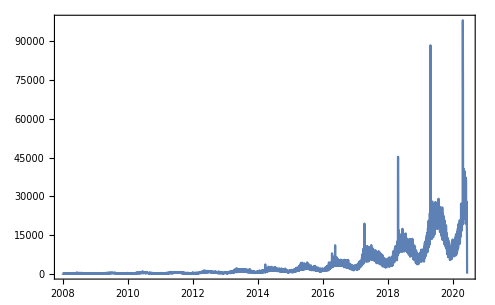

```mathematica
DateListPlot[tsClipped,PlotRange->All]
```

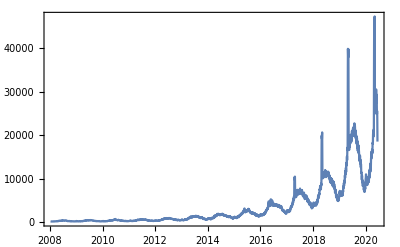

```mathematica
DateListPlot[MovingMap[Mean,tsClipped,Quantity[10, "Days"]],PlotRange->All]
```

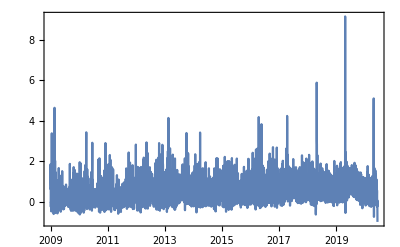

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]&,tsClipped,"Year"],PlotRange->All]
```

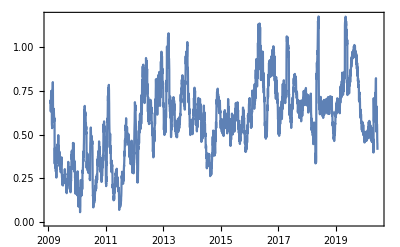

```mathematica
DateListPlot[MovingMap[Mean,MovingMap[(Last[#]-First[#])/First[#]&,tsClipped,"Year"],Quantity[30, "Days"]],PlotRange->All]
```

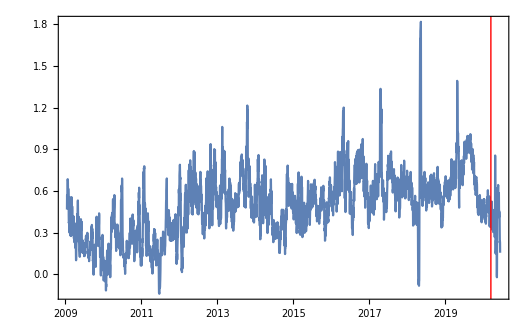

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]&,MovingMap[Mean,tsClipped,Quantity[15, "Days"]],"Year"],Epilog->{Red,InfiniteLine[{DateObject[{2020,3,15}],0},{0,1}]},PlotRange->All]
```